# Лабораторная работа №8

## Математические модели процессов диффузии частиц вещества

Мат. моделирование динамических процессов 1
БГУ, ММФ, 3 курс, 6 семестр
специальность Компьютерная математика и системный анализ
май 2022
ММФ, КМ и СА, доц. Лаврова О.А., доц. Щеглова Н.Л.

## Задание 1. Одномерное уравнение диффузии в неподвижной среде

### Концептуальная постановка задачи

[2, стр. 219, задача 9] Цилиндр длины l, заполненный воздухом при давлении и температуре окружающей среды, открывают с одного конца в начальный момент времени, и из окружающей атмосферы, где концентрация некоторого газа равна ϕ_0=const, начинается диффузия газа в цилиндр. Начальная концентрация газа в цилиндре равна 0. Площадь поперечного сечения цилиндра намного меньше длина цилиндра.

### Дополнительные теоретические сведения

Отметим, что аналогичная математическая модель строится для описания одномерного процесса передачи тепла на основании следующей концептуальной постановки задачи.

Концептуальная постановка задачи для процесса теплопроводности

На одном конце стержня длины l поддерживается постоянная температура u(x,0)=u_0=const, второй конец стержня теплоизолирован. Начальная температура стержня равна 0. Площадь поперечного сечения стержня намного меньше длина стержня, теплообмен на боковой поверхности отсутствует. Найдите распределение температуры u(x,t) стержня при 0<t<+∞.

### Задание 1.1 (Математическая модель)

Сформулируйте математическую модель в виде первой краевой задачи (начальное условие, граничное условие Дирихле на обоих концах цилиндра) для одномерного уравнения диффузии в неподвижной среде по концептуальной постановке задачи.

Математическая модель первой краевой задачи для одномерного уравнения диффузии в неподвижной среде

d_t u - D^2 d_x^2u = 0, 
0 < x < l,  0<t<+∞
D = const > 0 - коэффициент диффузии

Начальное условие одномерного уравнения диффузии в неподвижной среде

u(x,0)=0,    0 ≤ x ≤ l

Граничное условие Дирихле на обоих концах цилиндра одномерного уравнения диффузии в неподвижной среде

u(0,t)=u_0,    0<t<+∞
u(l,t)=0,    0<t<+∞

### Задание 1.2 (Аналитическое решение)

Постройте аналитическое решение математической модели c помощью метода разделения переменных, а также с помощью функции DSolve. 

Сравните графики построенных решений.

Аналитическое решение математической модели первой краевой задачи для одномерного уравнения диффузии в неподвижной среде

Решение данной задачи будем искать в виде u(x) = u^-(x) + v(x,t), где  u^-(x) - стационарная температура, а v(x,t) - отклонение от стационарной температуры.

Стационарную температуру u^-(x) будем искать в виде u^-(x) = B + A x при условиях u^-(0) = B = u_0  и u^-(l) =  B + A l = 0, тогда получаем
 u_0 + A l = 0   ==> A = - u_0/l. Подставляем найденные А и В в исходную функцию и получаем: 
 u^-(x) = u_0  - u_0/l х.
 
 Исходную задачу перепишем относительно функции отклонения от стационарной температуры, тогда:
d_t u^-(x) + d_t v(x,t)  - D^2 (d_x^2 u^-(x) + d_x^2 v(x,t))=0; (*)
0=u(x,0)=u^-(x) +v(x,0) ==> v(x,0)=u_0 -u_0/l х, 0 ≤ x ≤ l;
v(0,t)=0, 0<t<+∞
v(l,t)=0, 0<t<+∞
Учитывая, что стационарная температура u^-(x) не зависит явно от времени и учитывая полученную функцию u^-(x),  уравнение (*) можно записать в виде:
d_t v(x,t) - D^2  d_x^2 v(x,t)=0; (**)
Решение данной задачи будем искать в виде v(x, t) = X(x) T(t). Подставляем в уравнение и получаем, что
X(t) T’(t) = D^2 X ’’ (t) T(t)
Разделим обе части на X(x) T(t) и получаем 
(T'(t))/(D^2 T(t)) = (X'' (x))/(X (x)) = -λ,  где λ = const
Из последнего уравнения для переменной x с учётом граничных условий, получаем задачу Штурма-Лиувилля
X ’’(x) + λ X (x) = 0,
X(0) = 0 , X(l) = 0
Рассмотрим возможные случаи:
I. При λ < 0 общее решение последней задачи имеет вид X(x) = C_1 ⅇ^(√-λ x)+C_2 ⅇ^(-√-λx) . Подставляем в граничные условия:
C_1+C_2=0,
C_1 ⅇ^(√-λ l)+C_2 ⅇ^(-√-λl) = 0
Из первого уравнения выражаем C_2 = −C_1, подставляем во второе и получаем, что
C_1(ⅇ^(√-λ l)-ⅇ^(-√-λl))= 0
из которого получается, что C_1 = 0. А в таком случае, и C_2 = −C_1 = 0, и, таким образом, не существует не тривиальных решений.
II. При λ = 0 уравнение примет вид X” (x)= 0, а общее решение задачи, следовательно,  X(x) = C_1 + C_2 x. Подставляя граничные условия, получаем, что
C_2 = 0,  C_1 l + C_2 = 0, и, следовательно, C_2 = C_1 = 0, а значит не существует нетривиальных решений.
III. При λ > 0, общее решение имеет вид:
X(x)=C_1 cos(√λ x)+C_2 sin(√λ x)
Подставляем граничные условия и получаем систему:
C_1=0
	C_1 cos(√λ l)+C_2 sin(√λ l) =0
С учётом первого уравнения, второе уравнение перепишется следующим образом: 
C_2 sin(√λ l) =0
Отсюда получается, что sin(√λ l) =0, а значит√λ l = π n, n ϵ ℤ. Таким образом,
√λ = (π n)/l, X_n(x) = C_n sin((π n)/l x).
Полагая C_n = 1, получаем, что X_n(x) = sin((π n)/l x).
Будем искать решение этой задачи v(x,t) в виде ряда Фурье по собственным функциям sin((π n)/l x):
v(x,t)=∑_(n=1)^∞ T_n(t)X_n(x)=∑_(n=1)^∞ T_n(t)sin((π n)/l x)
Подставляя предполагаемую форму решения в исходное уравнение для v(x,t), будем иметь:
∑_(n=1)^∞ (T_n'(t)+D^2((π n)/l)^2 T_n(t))sin((π n)/l x)=0
Решая вышеприведенное уравнение функции T_n(t), получаем
 T_n'(t)+D^2((π n)/l)^2 T_n(t) = 0
 T_n(t)=C_n Exp(-D^2((π n)/l)^2 t)
 Тогда функция  v(x,t) и ее начальное условие примет следующий вид
v(x,t)=∑_(n=1)^∞ C_n Exp(-D^2((π n)/l)^2 t)sin((π n)/l x) 
v(x,0)=∑_(n=1)^∞ C_n sin((π n)/l x)=u_0 x/l -u_0, где 
C_n = 2/l(∫_0)^l u_0(σ-l)/l sin((π n)/l σ) d σ = 2 u_0(sin (π n)-π n)/(π^2 n^2)
 Исходя из этого, функция  v(x,t) получается следующей:
 v(x,t)=∑_(n=1)^∞ 2 u_0(sin (π n)-π n)/(π^2 n^2)Exp(-D^2((π n)/l)^2 t)sin((π n)/l x)
 Тогда аналитическое решение математической модели первой краевой задачи для одномерного уравнения диффузии в неподвижной среде представляется следующим образом:
  u(x,t)=u_0 -u_0/l х +2 u_0∑_(n=1)^∞ (sin (π n)-π n)/(π^2 n^2)Exp(-D^2((π n)/l)^2 t)sin((π n)/l x), 
где  0 < x < l,  0<t<+∞

Решение математической модели первой краевой задачи для одномерного уравнения диффузии в неподвижной среде при помощи DSolve

```mathematica
ClearAll[u]
DSolveValue[{D[u[x,t],t]-a^2 D[u[x,t],{x,2}]==0,u[x,0]==0,u[0,t]==u0,u[l,t]==0},u[x,t],{x,t}]
```

u0-(u0 x)/l-(2 (ⅇ^(-(a^2 π^2 t K[1]^2)/l^2) u0 Sin[(π x K[1])/l])/K[1]K[1]1∞)/π

Как можно заметить из результата, полученного при помощи DSolve, решение математической модели первой краевой задачи для одномерного уравнения диффузии в неподвижной среде немного отличается от решения, полученного при аналитическом решении. Проверим полученные результаты через графики построенных решений

```mathematica
ClearAll[uSol]
uSol[u0_,DD_,l_,n_]:=u0-u0/l x+Sum[(2 (Sin[π k]- π k) u0)/(π^2 k^2)Exp[-DD^2((π k)/l)^2 t]Sin[(π k)/l x],{k,1,n}]
```

```mathematica
ClearAll[uDSolve]
uDSolve[u0_,DD_,l_,n_]:=Quiet@(Flatten@Values@NDSolve[{D[u[x,t],t]-D[u[x,t],{x,2}]==0,u[x,0]==0,u[0,t]==u0,u[l,t]==0},u[x,t],{x,0,n},{t,0,n}])⟦1⟧
```

```mathematica
uSol[10,2,100,4]
```

10-x/10-(20 ⅇ^(-(π^2 t)/2500) Sin[(π x)/100])/π-(10 ⅇ^(-(π^2 t)/625) Sin[(π x)/50])/π-(20 ⅇ^(-(9 π^2 t)/2500) Sin[(3 π x)/100])/(3 π)-(5 ⅇ^(-(4 π^2 t)/625) Sin[(π x)/25])/π

```mathematica
uDSolve[10,2,100,4]
```

InterpolatingFunction[…][x,t]

```mathematica
uSol[10,2,100,4]/.{x->4,t->4}//N
```

6.79822

```mathematica
uDSolve[10,2,100,4]/.{x->4,t->4}
```

1.42652

```mathematica
Plot3D[uSol[10,2,120,100]/.{x->x0,t->t0},{x0,0,100},{t0,0,100},AxesLabel->{"x","t","u(x,t)"},ImageSize->Large]
```

-Graphics3D-

```mathematica
Plot3D[uDSolve[10,2,120,100]/.{x->x0,t->t0},{x0,0,100},{t0,0,100},AxesLabel->{"x","t","u(x,t)"},PlotRange->Full,ImageSize->Large]
```

-Graphics3D-

```mathematica
Plot3D[uDSolve[10,2,120,100]/.{x->x0,t->t0},{x0,0,100},{t0,0,4},AxesLabel->{"x","t","u(x,t)"},PlotRange->Full,ImageSize->Large]
```

-Graphics3D-

Как можно заметить из полученных выше графиков, аналитическое решение и решение, построенное через DSolve, отличаются как по полученным значениям, так и по построению графика. Однако, графики обеих решений наглядно показывают, что сходство между ними есть и причем при x→+∞, где 0 < x < l решение u(x,t) будет стремиться к 0. Соответственно, данные решения не будут значительно отличаться при больших значениях x

### Задание 1.3 (Анализ количества диффундировавшего газа)

Вычислите количество газа, диффундировавшего в цилиндр за время t.  Для этого вычислите интеграл от концентрации ϕ(x,t) по длине цилиндра. 

Постройте график зависимости количества диффундировавшего газа от времени t.

Количество газа, диффундировавшего в цилиндр

```mathematica
l=120;
gasQuantity1=Integrate[uSol[10,2,l,100],{x,0,l}];
```

```mathematica
l=120;
gasQuantity2=Integrate[uDSolve[10,2,l,100],{x,0,l}]
```

InterpolatingFunction[…][t]

```mathematica
Quiet@(gasQuantity1/.{t->100}//N)
gasQuantity2/.{t->100}
```

225.673

112.275

График зависимости количества диффундировавшего газа от времени t.

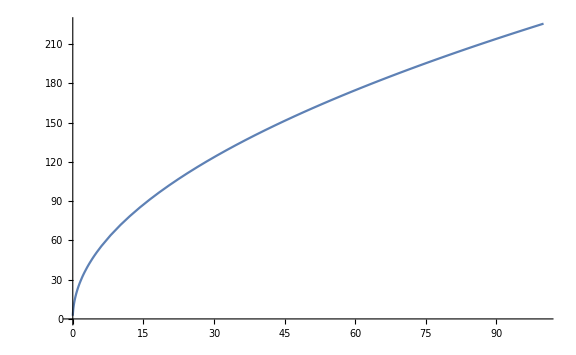

```mathematica
Plot[gasQuantity1/.{t->t0},{t0,0,100},ImageSize->Large]
```

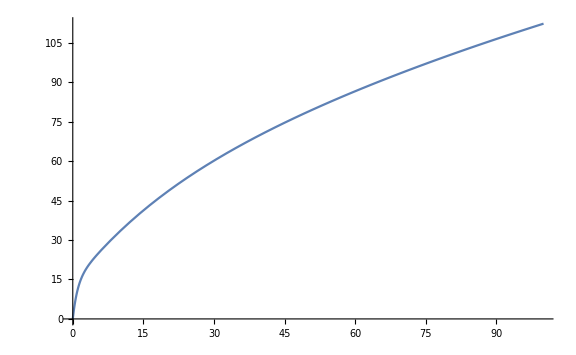

```mathematica
Plot[gasQuantity2/.{t->t0},{t0,0,100},ImageSize->Large]
```

Из полученных выше графиков можно заметить, что количество диффундировавшего газа увеличивается с увеличением времени t

## Задание 2. Математические модели пространственной популяционной динамики при случайном перемещении особей

Рассмотрим математическую модель популяционной динамики в предположении о случайном перемещении особей в ограниченной области проживания X=[0,l]. Математическую модель можно описать с помощью уравнения реакции-диффузии

(∂u(x,t))/(∂t)==D(∂^2 u(x,t))/(∂x^2)+k u (1-u),

где u(x,t)≥0 -- плотность особей популяции, 
x∈X=[0,l], 
D=const>0 -- характеризует скорость передвижения особей, 
k=const>0. Последнее слагаемое в правой части уравнения (1) регулирует изменение численности популяции и соответствует логистической модели.

Уравнение (1) называется уравнением Фишера - Колмогорова (1937) и является фундаментальным уравнением в биологии.

Дополнительно к уравнению (1) формулируется начальное условие u(x,0)=u_0(x) и однородное условие Дирихле на границе области, имитирующее проживание популяции на острове, u(0,t)=u(l,t)=0.

### Задание 2.1 (Устойчивоть положений равновесия)

Исследуйте устойчивость положений равновесия рассматриваемой модели с помощью фазового портрета стационарных решений.

Рассмотрим стационарные решения
u “ =-k/Du(1-u)
Уравнение соответствует динамической системе 2-го порядка
du/dx=v,
dv/dx=-k/Du(1-u)
Динамическая система имеет два положения равновесия для (u, v) : (0, 0) и (1, 0)
Линеаризуем динамическую систему в окрестности точки (0, 0)
d/dx(u
v)=(0 | 1
-k/D | 0)(u
v)
Тогда собственные значения матрицы будут следующими
det(-λ | 1
-k/D | -λ)=0;
λ^2+k/D=0 ;
λ=±ⅈ √(k/D)
Так как Re λ_i = 0, то метод линеаризации применять нельзя. Положение равновесия (0,0) может быть центром (всегда устойчивый) или фокусом (устойчивый или неустойчивый).

Линеаризуем динамическую систему в окрестности точки (1, 0). 
Для этого предварительно сделаем замену переменных ũ = u - 1.
(d ũ)/dx=v,
dv/dx=k/D ũ(1+ũ)

Или
d/dx(ũ
v)=(0 | 1
k/D | 0)(ũ
v);
Тогда собственные значения матрицы будут следующими
det(-λ | 1
k/D | -λ)=0;
λ^2-k/D=0 ;
λ=±√(k/D) - седло (неустойчивая точка) ==> неустойчивое положение равновесия

Фазовый портрет изучаемой динамической системы.
Для рассматриваемой модели биологически возможными являются решения, для которых u ≥ 0

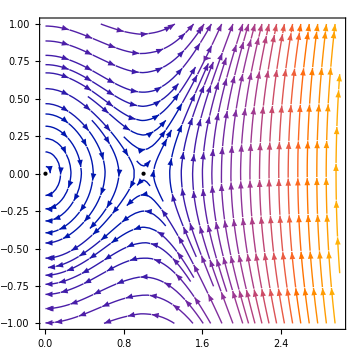

```mathematica
StreamPlot[{v,-u(1-u)},{u,0,3},{v,-1,1},Epilog->Point[{{0,0},{1,0}}],ImageSize->Medium]
```

Как можно заметить из фазового портрета выше, точка (0, 0) является центром, который всегда является устойчивым, а точка (1, 0) является седлом, которая всегда является неустойчивым

Для дальнейшего качественного анализа модели необходимо рассмотреть граничные условия. Для моделирования ситуации проживания на острове, когда проживание на границе области полагается невозможным, используются однородные условия Дирихле u(0) = u(l) = 0.

В окрестности точки (0,0) исходное уравнение принимает вид
u “ =-k/Du (модель пружинного осциллятора)
Общее решение может быть записано в виде
u(x) = A sin(√(k/D)x +ϕ)

Так как u(0)=0, то ϕ = 0
Так как u(l)=0, то  A sin(√(k/D)l ) = 0 ===> √(k/D)l = π ===> l* = π√(D/k)
Таким образом, при l=l* построено стационарное решение, которое не является решением вида u = 0. Следовательно, 

при l < l* не существует нетривиального стационарного решения, чтобы u(0) = u(l) = 0. Тогда u=0 устойчивое решение и популяция вымрет;

при l=l* решение модели стремится к стационарному решению вида  u(x) = A sin(π/lx );

при l ≥ l* популяция не вымирает.

### Задание 2.2 (Качественное поведение численного решения)

Постройте графики решений математической модели (1), построенных с помощью NDSolve, при k=1 с некоторым начальным условием u_0(x), близким к нулю, при различных размерах области X и различных значениях скорости передвижения особей D. 

Продемонстрируйте, что при недостаточном размере области l<l^*=π √(D/k)  популяция будет вымирать.

```mathematica
k=1;
u0=0.01;
Manipulate[
func=Quiet@(u/.NDSolve[{
D[u[x,t],t]==DD D[u[x,t],{x,2}]+k u[x,t] (1-u[x,t]),
u[x,0]==u0,u[0,t]==0,u[l,t]==0},
u,{x,0,l},{t,0,tend}])⟦1⟧;
Column[{If[l≥π √(DD/k),StringForm["``= l ≥ l^*= π√(D/k)= `` \nПопуляция не вымирает",NumberForm[l,4],NumberForm[N[π √(DD/k)],4]],
StringForm["``= l < l^*= π√(D/k)= `` \nПопуляция вымирает",NumberForm[l,4],NumberForm[N[π √(DD/k)],4]]
],
Row[{
Plot3D[func[x,t],{x,0,l},{t,0,tend},PlotRange->All,AxesLabel->Automatic,ImageSize->Medium],
Manipulate[
Plot[func[x,tnew],{x,0,l},ImageSize->Medium,AxesLabel->Automatic,PlotRange->{{Automatic,Automatic},{0,1}}],
{{tnew,5,"t"},0,tend,Appearance->"Labeled"}]
}]
}],
{{l,10},1,100,Appearance->"Labeled"},
{{DD,2,"D"},0,10,0.1,Appearance->"Labeled"},
{{tend,50,"t_end"},1,100,Appearance->"Labeled"}
]
```

### Задание 2.3 (Качественный анализ модели Скеллама)

Для модели Скеллама вида

(∂u(x,t))/(∂t)==D(∂^2 u(x,t))/(∂x^2)+k u ,

с однородными условиями Дирихле на границе области также справедливо утверждение, что при недостаточном размере области l<l^*=π √(D/k)  популяция будет вымирать. Проверьте это утверждение.

```mathematica
u0=0.01;
Manipulate[
func=Quiet@(u/.NDSolve[{
D[u[x,t],t]==DD D[u[x,t],{x,2}]+k u[x,t] ,
u[x,0]==u0,u[0,t]==0,u[l,t]==0},
u,{x,0,l},{t,0,tend}])⟦1⟧;
Column[{If[l≥π √(DD/k),StringForm["``= l ≥ l^*= π√(D/k)= `` \nПопуляция не вымирает",NumberForm[l,4],NumberForm[N[π √(DD/k)],4]],
StringForm["``= l < l^*= π√(D/k)= `` \nПопуляция вымирает",NumberForm[l,4],NumberForm[N[π √(DD/k)],4]]
],
Row[{
Plot3D[func[x,t],{x,0,l},{t,0,tend},PlotRange->All,AxesLabel->Automatic,ImageSize->Medium],
Manipulate[
Plot[func[x,tnew],{x,0,l},ImageSize->Medium,AxesLabel->Automatic,PlotRange->{{Automatic,Automatic},{0,1}}],
{{tnew,5,"t"},0,tend,Appearance->"Labeled"}]
}]
}],
{{l,10},1,100,Appearance->"Labeled"},
{{k,1},0,1,Appearance->"Labeled"},
{{DD,2,"D"},0,10,0.1,Appearance->"Labeled"},
{{tend,50,"t_end"},1,100,1,Appearance->"Labeled"}
]
```

### Задание 2.4 (Качественный анализ двумерной модели Скеллама)

Для двумерной модели Скеллама вида

(∂u(x,y,t))/(∂t)==D((∂^2 u(x,y,t))/(∂x^2)+(∂^2 u(x,y,t))/(∂y^2))+k u ,

в квадратной области X=[0,l]×[0,l] с однородными условиями Дирихле на границе области необходимо продемонстрировать существование критического размера области l^*, такого, что при l<l^* популяция будет вымирать, на основе интерактивной визуализации решения модели (3) при k=1.

```mathematica
k=1;
u0=0.01;
Manipulate[
func=Quiet@(u/.NDSolve[{
D[u[x,y,t],t]==DD( D[u[x,y,t],{x,2}] +D[u[x,y,t],{y,2}])+k u[x,y,t],
u[x,y,0]==u0,u[0,y,t]==0,u[l,y,t]==0,u[x,0,t]==0,u[x,l,t]==0},
u,{x,0,l},{y,0,l},{t,0,tend}])⟦1⟧;
ρ=Quiet@Integrate[func[x,y,t],{x,0,l},{y,0,l}];
Column[{If[l≥π √((2DD)/k),StringForm["``= l ≥ l^*= π√((2  D)/k)= `` \nПопуляция не вымирает",NumberForm[l,4],NumberForm[N[π √((2DD)/k)],4]],
StringForm["``= l < l^*= π√((2  D)/k)= `` \nПопуляция вымирает",NumberForm[l,4],NumberForm[N[π √((2 DD)/k)],4]]
],
Row[{
Plot[ρ/.{t->t0},{t0,0,tend},PlotRange->All,ImageSize->Large]
}]
}],
{{l,4},1,100,Appearance->"Labeled"},
{{DD,2,"D"},0,10,0.1,Appearance->"Labeled"},
{{tend,50,"t_end"},1,100,1,Appearance->"Labeled"}
]
```

## Задание 3 (необязательное). Математическая модель преобразования сигнала в аксоне

[5, стр. 117, упр. 4.5.5] Рассмотрим математическую модель преобразования сигнала в аксоне в виде уравнения реакции-диффузии

(∂u(x,t))/(∂t)==(∂^2 u(x,t))/(∂x^2)+(u-1/2) (1-u) u

для потенциала мембраны u(x,t), 0≤x≤l, где l -- заданная длина аксона, c начальным условием u(x,0)=u_0(x) и с однородными условиями Неймана на границах аксона

(∂u(0,t))/(∂x)==0, (∂u(l,t))/(∂x)==0.

### Задание 3.1 (Устойчивость положений равновесия)

Исследуйте устойчивость положений равновесия рассматриваемой модели с помощью фазового портрета стационарных решений.

Попробуйте сформулировать биологический смысл построенных стационарных решений.

## Задание 4. Одномерное стационарное уравнение диффузии с точечным источником

### Задание 4.1 (Математическая модель)

Сформулируйте математическую модель для описания процесса выброса химического вещества (аэрозоля) промышленным предприятием на основании стационарного одномерного процесса диффузии вещества при условиях, что

коэффициент диффузии постоянный, D(x)=const>0;

скорость потока воздушных масс атмосферы постоянная, u(x)=const;

процесс поглощения атмосферой химического вещества задается коэффициентом σ=const>0;

точечный источник вещества мощности Q=const>0, выбрасывающий в атмосферу аэрозоль, расположен в точке x=x_0.

концентрация вещества ϕ зависит от значений переменныx x и t, т.е. процесс диффузии является одномерным ϕ = ϕ(x,t)

Математическая модель процесса выброса химического вещества (аэрозоля) промышленным предприятием на основании стационарного одномерного процесса диффузии вещества

D (d^2 ϕ)/dx^2 - σ ϕ + u dϕ/dx= - Q δ (x-x_0),  где   x ϵ  ℝ

При этом полагаем ограниченность решения в области определения, то есть
ϕ → 0  при x  → ±∞

### Задание 4.2 (Аналитическое решение)

Постройте аналитическое решение математической модели.

```mathematica
SetDirectory@CurrentValue@"NotebookDirectory"
```

D:\ММДС

```mathematica
Import["LR8T4.2.pdf",{"PageImages",1}]
```

-Graphics-

### Задание 4.3 (Динамическая визуализация)

Осуществите динамическую визуализацию решения модели с интерактивным изменением параметров модели D,  u,σ, Q, x_0.

```mathematica
Manipulate[
Plot[
If[x≤x0,Q/(√(u^2+4 DD σ))Exp[(-u+√(u^2+4DD σ))/(2DD)(x-x0)],Q/(√(u^2+4 DD σ))Exp[(-u-√(u^2+4DD σ))/(2DD)(x-x0)]],
{x,-20,20},PlotRange->1.5,ImageSize->Large,AxesLabel->{"x","φ(x)"}],
{{DD,1,"D"},0.1,20,0.1,Appearance->"Labeled"},
{{u,0},-10,10,0.1,Appearance->"Labeled"},
{{σ,1},0.1,10,0.1,Appearance->"Labeled"},
{{Q,1},0.1,10,0.1,Appearance->"Labeled"},
{{x0,0,"x_0"},-20,20,0.1,Appearance->"Labeled"}]
```

Исходя из вышеприведённого графика, можно сделать следующие выводы параметров модели :
   D - коэффициент диффузии - мера того, насколько эффективно частицы вещества движутся из области с высокой концентрацией в область с низкой 		концентрацией. На модели показывается как увеличение или уменьшение значение функции по оси OY;
   u - скорость потока воздушных масс атмосферы влияет на количество распространения химического вещества в среде, причем данный параметр 		очень зависит от знака константы, так как от этого параметра показывается интенсивность распределения   химического вещества в среде; 
   σ - процесс поглощения атмосферой химического вещества - мера того, насколько быстро поглощается атмосферой частицы химического вещества 		движутся из области с высокой концентрацией в область с низкой концентрацией. На модели показывается как увеличение или уменьшение 	значение функции по оси OY;
   Q - точечный источник вещества мощности, выбрасывающий в атмосферу аэрозоль, расположенный в точке x=x_0. На модели показывается как 			увеличение или уменьшение  значение функции по оси OY;
   x_0 -  начальное расположение источника выброса химического вещества в воздух.

## Литература

[1] В. И. Корзюк. Уравнения математической физики: учеб. пособие. -- Минск.: БГУ, 2011.

[2] А. Н. Тихонов, А. А. Самарский. Уравнения математической физики. -- М.: Наука, 1977.

[3] Г. И. Марчук. Математическое моделирование в проблеме окружающей среды. -- М.: Наука, 1982.

[4] Л. А. Петросян, В. В. Захаров. Введение в математическую экологию. -- Л.: Изд-во Ленингр. ун-та, 1986.

[5] G. Vries, T. Hillen, M. Lewis, J. Mueller, B. Schoenfisch. A course in mathematical biology: quantitative modeling with mathematical and computational methods. SIAM, 2006.